```mathematica
Remove["Global`*"];
PDF1 = s/(2*R^2);

Hinverse = 2*R*Sin[d / (R * 2)];
DHinverse = Simplify[Dt[Hinverse, d , Constants ->{R}]] ;
PDF2 = FullSimplify[Function[s, Evaluate[PDF1]]   [2*R*Sin[d / (R * 2)]]*DHinverse]
```

Sin[d/R]/(2 R)

```mathematica
a={d∈Reals,R∈Reals, d >0, R>= 0 , d ≤ π*R };
```

```mathematica
CDF2 = Simplify[Integrate[PDF2, d] -Function[d, Evaluate[Integrate[PDF2, d]]] [0]]
```

Sin[d/(2 R)]^2

```mathematica
MEAN = FullSimplify[Integrate [d * PDF2, {d, 0, π * R}, Assumptions->a] ,a]
```

(π R)/2

```mathematica
VAR= Integrate [PDF2 * (d - MEAN)^2,{d, 0, π * R}]
```

1/4 (-8+π^2) R^2

```mathematica
CForm[MEAN]
```

(Pi*R)/2.

```mathematica
CForm[VAR]
```

((-8 + Power(Pi,2))*Power(R,2))/4.

```mathematica
TeXForm[PDF2]
```

\frac{\sin \left(\frac{d}{R}\right)}{2 R}

```mathematica
TeXForm[CDF2]
```

\sin ^2\left(\frac{d}{2 R}\right)

```mathematica
CForm[PDF2]
```

Sin(d/R)/(2.*R)

```mathematica
CForm[CDF2]
```

Power(Sin(d/(2.*R)),2)

```mathematica
R=2;
```

```mathematica
4
```

4

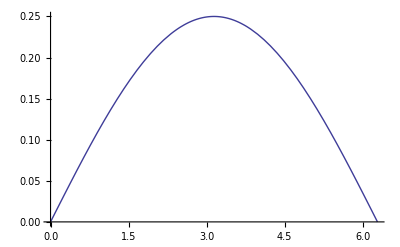

```mathematica
Plot[{PDF2},{d,0,π*R}]
```

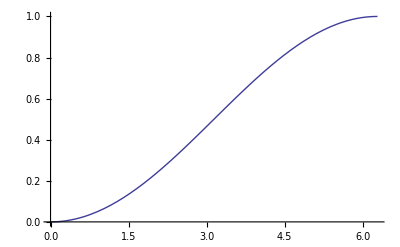

```mathematica
Plot[{CDF2},{d,0,π*R}]
```